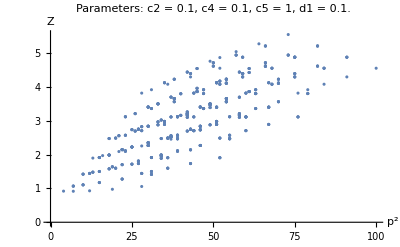

```mathematica
c1 = 0;
c2 = .1; 
c3 = 0;
c4 = .1; 
c5 = .1; 
d1 = .1;
L = 16;
Lt = 48;
Z[μ_] := 1;
Zhyp[ρ_] := Z[ρ . ρ] + c1 * (ρ[[3]] - ρ[[4]]) + c2 * (ρ . ρ) + c3 * ρ[[4]]^2  + c4 * (ρ[[1]]^4 + ρ[[2]]^4 + ρ[[3]]^4 + ρ[[4]]^4) / (ρ . ρ) + c5 * (ρ . ρ) * Log[ρ . ρ] + d1 / (ρ . ρ);
ptwid[p1_, p2_, p3_, p4_] := {Sin[2*Pi * p1 / L], Sin[2*Pi*p2 / L], Sin[2*Pi*p3/L], Sin[2*Pi*p4/Lt]};
Ztable = Table[{i^2 + j^2 + k^2 + l^2, Zhyp[ptwid[i, j, k, l]]},
 {i, 1, 5}, {j, 1, 5}, {k, 1, 5}, {l, 1, 5}];
Zlist = Flatten[Ztable, 3];
ListPlot[Zlist, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Parameters: c2 = ``, c4 = ``, c5 = ``, d1 = ``. ",  c2, c4, c5, d1]]
```

{{4.,2.32513},{5.,1.17239},{8.,0.956235},{5.,1.17239},{6.,0.959232},{9.,1.00929},{8.,0.956235},{9.,1.00929},{12.,1.31688},{5.,1.17239},{6.,0.959232},{9.,1.00929},{6.,0.959232},{7.,0.917135},{10.,1.10706},{15.,1.50244},{9.,1.00929},{10.,1.10706},{13.,1.48184},{18.,1.98844},{15.,1.50244},{18.,1.98844},{23.,2.5747},{8.,0.956235},{9.,1.00929},{12.,1.31688},{9.,1.00929},{10.,1.10706},{13.,1.48184},{18.,1.98844},{12.,1.31688},{13.,1.48184},{16.,1.97248},{21.,2.56168},{28.,2.82869},{18.,1.98844},{21.,2.56168},{26.,3.215},{33.,3.50503},{28.,2.82869},{33.,3.50503},{40.,3.80346},{15.,1.50244},{18.,1.98844},{23.,2.5747},{18.,1.98844},{21.,2.56168},{26.,3.215},{33.,3.50503},{23.,2.5747},{26.,3.215},{31.,3.92271},{38.,4.23267},{33.,3.50503},{38.,4.23267},{45.,4.55002},{28.,2.82869},{33.,3.50503},{40.,3.80346},{33.,3.50503},{38.,4.23267},{45.,4.55002},{40.,3.80346},{45.,4.55002},{52.,4.87443}}

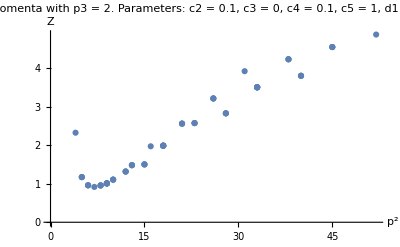

```mathematica
psub = Map[IntegerPart, Import["/Users/theoares/lqcd/npr_momfrac/analysis_output/psub_2_17999.txt", "CSV"]];
Zsubtable = Table[{psub[[i]][[1]]^2 + psub[[i]][[2]]^2 + psub[[i]][[3]]^2 + psub[[i]][[4]]^2,Zhyp[ptwid[
psub[[i]][[1]], 
psub[[i]][[2]], 
psub[[i]][[3]], 
psub[[i]][[4]]
]]},{i, 1, Length[psub]}];
Zsublist = Flatten[Zsubtable, 3];
Print[N[Zsubtable]]
ListPlot[Zsubtable, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Momenta with p3 = 2. Parameters: c2 = ``, c3 = ``, c4 = ``, c5 = ``, d1 = ``. ",  c2, c3, c4, c5, d1]]
```

```mathematica
β = 6.1;
g = Sqrt[6 / β];
S[ρ_, n_] := ρ[[1]]^n + ρ[[2]]^n + ρ[[3]]^n + ρ[[4]]^n;
Zvb[ρ_] := 1 + g^2 * (4/3) / (16*Pi^2)*(
5.78101 - 8/3 * Log[S[ρ, 2]] + 4/9 * S[ρ, 4] / (S[ρ, 2]^2) + S[ρ, 2] * (-.56888 + 1/30 * Log[S[ρ, 2]]) + S[ρ, 4] / S[ρ, 2] * (-.51323 + 19/30 * Log[S[ρ, 2]]) + 71 / 270 * S[ρ, 4]^2 / (S[ρ, 2]^3) + 164/135*S[ρ, 6] / (S[ρ, 2]^2)
);

Zvbtable = Table[{i^2 + j^2 + k^2 + l^2, Zvb[ptwid[i, j, k, l]]},
 {i, 1, 5}, {j, 1, 5}, {k, 1, 5}, {l, 1, 5}];
Zvblist = Flatten[Zvbtable, 3];
ListPlot[Zvblist, AxesLabel->{p^2, Z}, PlotLabel->StringForm["Perturbative corrections to Z at β = ``. ", β]]
```